```mathematica
45
```

45

```mathematica
<<CNNeuralCore.m
```

Set::write: Tag BatchSize in SyntaxInformation[BatchSize] is Protected.

```mathematica
trainingSet=Import["C:\\Users\\julian\\ImageDataSets\\FaceScrub\\TrainingSet.mx"];
```

```mathematica
trainingSet[[3,1]]
```

-Graphics-

```mathematica
leftEye=ImageTake[trainingSet[[3,1]],{14-3,14+3},{12-3,12+3}]
```

-Graphics-

```mathematica
Image[1-ImageData[ImageCorrelate[trainingSet[[4,1]],leftEye,NormalizedSquaredEuclideanDistance]]]
```

-Graphics-

```mathematica
transformedDataSet=Map[Image[1-ImageData[ImageCorrelate[#[[1]],leftEye,NormalizedSquaredEuclideanDistance]]]->#[[2]]&,trainingSet[[10;;1010]]];
```

```mathematica
transformedDataSet[[50;;55]]
```

{-Graphics-→0,-Graphics-→0,-Graphics-→1,-Graphics-→1,-Graphics-→0,-Graphics-→1}

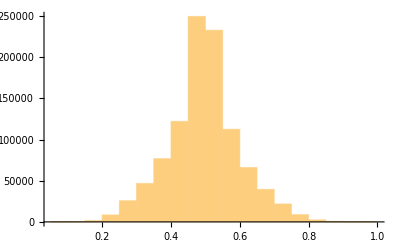

```mathematica
Histogram[Map[ImageData,transformedDataSet[[10;;-1,1]]]//Flatten]
```

```mathematica
trF=Map[
PDF[NormalDistribution[0.82,.03],ImageData[#[[1]]]]/
PDF[NormalDistribution[0.5,.03],ImageData[#[[1]]]]
->#[[2]]&,transformedDataSet];trF//Dimensions
```

{1001}

```mathematica
trF[[43]];
```

```mathematica
CNForwardPropogateLayer[MyLog,x_]:=Log[x]
```

```mathematica
CNBackPropogateLayer[MyLog,postLayerDeltaA_,inputs_,_]:=
  postLayerDeltaA/inputs;
```

```mathematica
CNLayerWeightPlus[MyLog,grad_]:=MyLog;
```

```mathematica
CNGradLayer[MyLog,layerInputs_,layerOutputDelta_]:={};
```

```mathematica
net={
ConvolveFilterBankToFilterBank[{
ConvolveFilterBankTo2D[
0,{Table[1/1024,{32},{32}],Table[0,{32},{32}]}],
ConvolveFilterBankTo2D[
0,{Table[0,{32},{32}],Table[1./1024,{32},{32}]}]
}],
AdaptorFilterBankTo1D[2,1,1],
MyLog,
FullyConnected1DToScalar[0,{-1,+1}],
Logistic
};
```

```mathematica
net={
Convolve2D[0,Table[(1./1024),{32},{32}]],
AdaptorFilterBankTo1D[1,1,1],
FullyConnected1DToScalar[0,{1}],
MyLog,
Logistic
};
```

```mathematica
A
```

```mathematica
CNForwardPropogate[ trF[[1;;5,1]], net]
```

{1.,1.,1.,1.72151×10^-12,1.}

```mathematica
net;
```

```mathematica
CNMiniBatchTrainModel[ net, trF[[1;;900]],CNCrossEntropyLoss,{MaxEpoch->20000,LearningRate->.0000001,ValidationSet->trF[[901;;-1]]}]
```

Batch Training Loss:

NNGrad::Dimensions of outputs and targets should match

$Aborted